```mathematica
momentum=1.99285191545*10^-24;
time= 2.4188843265864*10^-17;
freq=1/time;
energyIneV=27.211386245988;
```

```mathematica
1.1401649572210201*ℏovera0
```

2.27218×10^-24

```mathematica
SetDirectory[StringJoin[ NotebookDirectory[],"results/material=WernerBi/a=1.00nm/b_scan_for_v=0.5c/20250419_154448/Lmax=8"]]
```

/media/george/Almacenamiento1/Storage/8-Momentum Transfer from electrons to NPs/LMTsolver/results/material=WernerBi/a=1.00nm/b_scan_for_v=0.5c/20250419_154448/Lmax=8

```mathematica
FileNames[]
```

{dpdwx_WernerBi_v0.5c_b11nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b12nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b1.5nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b2.4nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b3.3nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b4.2nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b5.1nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b6nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b7.9nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b7nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b8.8nm_a1nm_20250419_154448.dat,dpdwx_WernerBi_v0.5c_b9.7nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b11nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b12nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b1.5nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b2.4nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b3.3nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b4.2nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b5.1nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b6nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b7.9nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b7nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b8.8nm_a1nm_20250419_154448.dat,dpdwz_WernerBi_v0.5c_b9.7nm_a1nm_20250419_154448.dat,DPx_WernerBi_v0.5c_a1nm_L8_.dat,DPz_WernerBi_v0.5c_a1nm_L8_.dat,error_DPx_WernerBi_v0.5c_a1nm_L8_.dat,error_DPz_WernerBi_v0.5c_a1nm_L8_.dat,simulation_parameters.txt}

```mathematica
FileNames[][[3]]
FileNames[][[15]]
FileNames[][[-5]]
```

dpdwx_WernerBi_v0.5c_b1.5nm_a1nm_20250419_154448.dat

dpdwz_WernerBi_v0.5c_b1.5nm_a1nm_20250419_154448.dat

DPx_WernerBi_v0.5c_a1nm_L8_.dat

```mathematica
dataperpendicular=Import[FileNames[][[-5]]];
```

```mathematica
spectraldataperpendicular=Import[FileNames[][[3]]];spectraldataparallel=Import[FileNames[][[15]]];
```

```mathematica
spectraldataperpendicular[[2]]
```

{0.5,1.5,3.57477×10^-6,0.000117858,-3.14881×10^-15,1.91138×10^-18,-1.89667×10^-18,1.75457×10^-16,-1.75478×10^-16}

```mathematica
dpdwx={};
For[i=2,i<=Length[spectraldataperpendicular],i++,
AppendTo[dpdwx,{spectraldataperpendicular[[i]][[3]]*energyIneV,Total[spectraldataperpendicular[[i]][[4;;]]]*momentum*time}]
]
dpdwz={};
For[i=2,i<=Length[spectraldataparallel],i++,
AppendTo[dpdwz,{spectraldataparallel[[i]][[3]]*energyIneV,Total[spectraldataparallel[[i]][[4;;]]]*momentum*time}]
]
```

```mathematica
spectraldataperpendicular[[1]]
```

{vv,b,w(au),dpEdwxInt,dpHdwxInt,dpEdwxScat,dpHdwxScat,dpEdwxExt,dpHdwxExt}

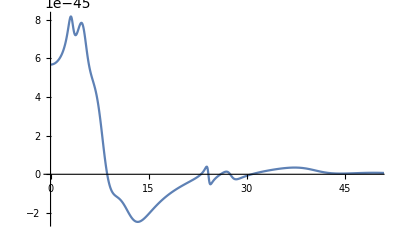

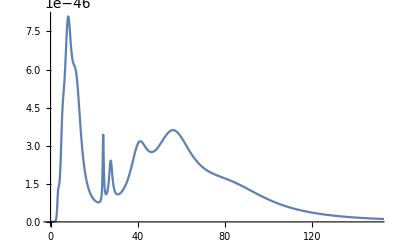

```mathematica
ListPlot[dpdwx,Joined->True,PlotRange->{{0,50},Automatic}]
ListPlot[dpdwz,Joined->True,PlotRange->{{0,150},Automatic}]
```

```mathematica
dataperpendicular[[1]]
```

{vv,b,DPExInt,DPHxInt,DPExScat,DPHxScat,DPExExt,DPHxExt,DPxTot}